## Modèle TBR

### Paramètres connues du système

```mathematica
L=0.99 (*m*); (*hauteur du réacteur*)
d=0.18 (*m*);(*diamètre de la colonne*)
Ω= Pi (d/2)^2(*m.b2*); (*surface de la colonne*)
dp=2.5 10^-2(*m*); (*diamètre éléments de garnissage*)
Rg=8.314(*kg m.b2 s^-2 K^-1 mol^-1*); (*constante gaz parfait*)
Tin=25+273.15 (*K*); (*température de travail*)
Pin=101325(*Pa*); (*pression de travail*)
Patm=1(*atm*);

Hco2=3.4 10^1 (*mol/m.b3/atm*); (*constante de Henry du CO2 dans l'eau à 25°C*)
Hh2=7.8 10^-1(*mol/m.b3/atm*); (*Constante de Henry de l'H2 dans l'eau à 25°C*)
(*Source: https://www.ready.noaa.gov/documents/TutorialX/files/Chem_henry.pdf*)
```

### Paramètres à exprimer

```mathematica
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)
Vsg[Qg_]:=Qg/(Ω(1-ϵs))(*m/s*);(*gas superficial velocity*)
Vsl[Ql_]:= Ql/(Ω(1-ϵs))(*m/s*);(*liquide superficial velocity*)

(*Source : Book,CHEMICAL REACTORS From Design to Operation*)
τcl[Ql_,ϵs_] :=(L(1-ϵs))/(Ql/Ω);(*temps lié à la convection liquide*)
τcg[Qg_,ϵs_]:=(L(1-ϵs))/(Qg/Ω) ;(*temps lié à la convection gazeuse*)
τdl[Ql_,ϵs_]:=100(L(1-ϵs))/(Ql/Ω); (*temps lié à la diffusion numérique liquide*)
τdg[Qg_,ϵs_] := 100(L(1-ϵs))/(Qg/Ω); (*temps lié à la diffusion numérique liquide*)
n = 100; (*nombre d'interval de l'axe discrétisé*)
Δ = 1/n;(*Taille d'un interval*)
ψ=5;
```

## Equations

```mathematica
Absol[Ql_,Qg_,ϵl_,ϵg_,ϵs_,klco2_,klh2_]:=(
(*Inconnues*)
CO2l=Table[Cco2[i][t],{i,1,n-1}];
CO2g=Table[yco2[i][t],{i,1,n-1}];
H2l=Table[Ch2[i][t],{i,1,n-1}];
H2g=Table[yh2[i][t],{i,1,n-1}];
(*CI t=0*)
ci1=Table[Cco2[i][0]==0,{i,1,n-1}];
ci2=Table[yco2[i][0]==0,{i,1,n-1}];
ci3=Table[Fg[i][0]==0,{i,1,n-1}];
ci4=Table[Ch2[i][0]==0,{i,1,n-1}];
ci5=Table[yh2[i][0]==0,{i,1,n-1}];
(*Conditions initiales en z=0*)
Cco2[n][t_]=Cco2[0][t];
yco2[0][t_]=0.2;
Fg[0][t_]=Pin/(Rg Tin) Qg;
Ch2[n][t_]=Ch2[0][t];
yh2[0][t_]=0.8;
(*Termes de réaction*)
rH2= 3.88*10^-5;(*mol/m.b3/s*)
rCO2= 9.69*10^-6;(*mol/m.b3/s*)
y0=0.001;(*mol/m.b3*)
y1=0.004;(*mol/m.b3*)
κ=10000;(*constante*)

(*Equations*)eq1=
Table[ϵl Cco2[i]'[t]==1/τcl[Ql,ϵs] (Cco2[i][t]-Cco2[i-1][t])/Δ+1/τdl[Ql,ϵs] (Cco2[i+1][t]-2Cco2[i][t]+Cco2[i-1][t])/Δ^2+ klco2 (Hco2 Patm yco2[i][t]-Cco2[i][t])
-rCO2 (1/(1+Exp[-κ*(Cco2[i][t]-y0)])),{i,1,n-1}]/.{Cco2[0][t]->Cco2[1][t]};

eq2=
Table[ϵg Pin/(Rg Tin)yco2[i]'[t]==-1/(Ω L)(Fg[i][t] (yco2[i][t]-yco2[i-1][t])/Δ+yco2[i][t] (Fg[i][t]-Fg[i-1][t])/Δ)+1/τdg[Qg,ϵs] (yco2[i+1][t]-2yco2[i][t]+yco2[i-1][t])/Δ^2 Pin/(Rg Tin)
- klco2(Hco2 Patm yco2[i][t]-Cco2[i][t]),{i,1,n-1}]/.{yco2[n][t]->yco2[n-1][t]};

eq3=
	Table[Fg[i][t]=- Ω L Δ ( klco2(Hco2 Patm yco2[i][t]-Cco2[i][t])+  klh2(Hh2 Patm yh2[i][t]-Ch2[i][t]))+Fg[i-1][t],{i,1,n-1}];

eq4=
Table[ϵl Ch2[i]'[t]==1/τcl[Ql,ϵs] (Ch2[i][t]-Ch2[i-1][t])/Δ+1/τdl[Ql,ϵs] (Ch2[i+1][t]-2Ch2[i][t]+Ch2[i-1][t])/Δ^2
+ klh2(Hh2 Patm yh2[i][t]-Ch2[i][t])-rH2 (1/(1+Exp[-κ*(Ch2[i][t]-y1)])) ,{i,1,n-1}]/.{Ch2[0][t]->Ch2[1][t]}; 

eq5=
Table[ϵg Pin/(Rg Tin)yh2[i]'[t]==-1/(Ω L) (Fg[i][t] (yh2[i][t]-yh2[i-1][t])/Δ+yh2[i][t] (Fg[i][t]-Fg[i-1][t])/Δ)+1/τdg[Qg,ϵs] Pin/(Rg Tin)(yh2[i+1][t]-2yh2[i][t]+yh2[i-1][t])/Δ^2
- klh2 (Hh2 Patm yh2[i][t]-Ch2[i][t]),{i,1,n-1}]/.{yh2[n][t]->yh2[n-1][t]};


sol =NDSolve[Join[eq1,eq2,eq4,eq5,ci1,ci2,ci4,ci5 ],Join[CO2l,CO2g,H2l, H2g],{t,0,ψ τcg[Qg,ϵs]}][[1]];
);
```

```mathematica
Print["La concentration de CO2 à saturation est de : ",Hco2 Patm yco2[0][t],"mol/m.b3"];
Print["La concentration d'H2 à saturation est de : ",Hh2 Patm yh2[0][t],"mol/m.b3"];
```

La concentration de CO2 à saturation est de : 34. yco2[0][t]mol/m.b3

La concentration d'H2 à saturation est de : 0.78 yh2[0][t]mol/m.b3

```mathematica
Qg1=(50 10^-6)/60;Ql1=(3.5 10^-3)/60;ϵs=0.086;
Absol[Ql1,Qg1,0.039,0.89,0.086,0.0265/60,0.071/60]
```

Analyse des transferts

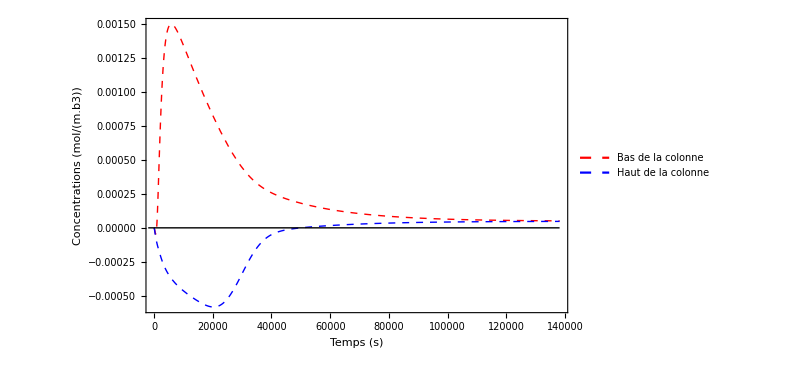

```mathematica
Plot[{(0.0265/60(Hco2 Patm yco2[10][t]-Cco2[5][t])+0.071/60 (Hh2 Patm yh2[10][t]-Ch2[10][t]))/. sol,(0.0265/60(Hco2 Patm yco2[n-10][t]-Cco2[n-10][t])+0.071/60(Hh2 Patm yh2[n-10][t]-Ch2[n-10][t]))/. sol},{t,0,ψ τcg[Qg1,ϵs]},PlotStyle->{Directive[Red,Dashed,Thick],Directive[Blue,Dashed,Thick]},PlotLegends->Placed[{"Bas de la colonne","Haut de la colonne"},{Scaled[{0.95,0.95}],{Right,Top}}],
Frame->True,PlotRange->All,FrameLabel->{"Temps (s)","Concentrations (\!\(\*FractionBox[\(mol\), \(m.b3\)]\))"},FrameStyle->Directive[Black,Thick],
BaseStyle->{FontSize->14},
AxesStyle->Directive[Black,Thick],
ImageSize->600,
Epilog->{Directive[Black,Thick],Line[{{-2000,0},{ ψ τcg[Qg1,ϵs],0}}]}]
```

InterpolatingFunction::dmval: Input value {-134228.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-22156.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4078.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

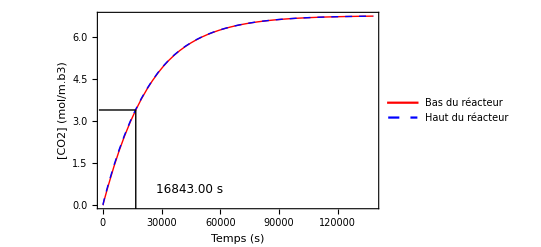

```mathematica
csatCO2=Hco2 Patm 0.2;
t50CO2=t/. FindRoot[(Cco2[10][t]/. sol)==Hco2 Patm 0.2/2,{t,0.5 ψ τcg[Qg1,ϵs]}];

(*Trouver le temps où Cco2 atteint 50 % de la saturation pour la première courbe*)
Plot[{Cco2[10][t]/. sol,Cco2[n-10][t]/. sol},{t,0,ψ τcg[Qg1,ϵs]},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"Temps (s)","[CO2] (mol/m.b3)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick]},Epilog->{Directive[Black],Line[{{t50CO2,-2},{t50CO2,csatCO2/2}}],Line[{{-2000,csatCO2/2},{t50CO2,csatCO2/2}}],Text[Style[ToString[NumberForm[t50CO2,{5,2}]]<>" s",12,Black],{t50CO2+0.2 ψ τcg[Qg1,ϵs],csatCO2/12},{1,0}]}]
```

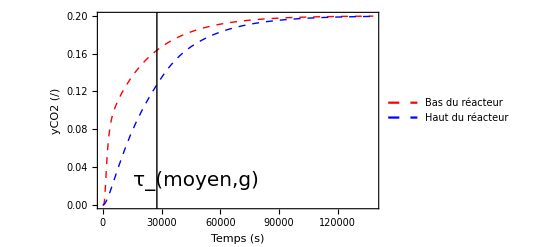

```mathematica
Plot[{yco2[10][t]/. sol,yco2[n-10][t]/. sol},{t,0,ψ τcg[Qg1,ϵs]},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"Temps (s)","yCO2 (/)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotStyle->{Directive[Red,Dashed,Thick],Directive[Blue,Dashed,Thick]},Epilog->{Directive[Black],Line[{{τcg[Qg1,ϵs],-0.1},{τcg[Qg1,ϵs],1.1}}],Text[Style["\!\(\*SubscriptBox[\(τ\), \(moyen,g\)]\)",20,Black],{τcg[Qg1,ϵs]+20000,0.025},{0,0}]}]
```

0.624

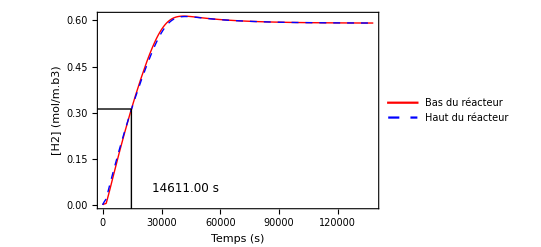

```mathematica
csatH2=Hh2 Patm 0.8
t50H2=t/. FindRoot[(Ch2[10][t]/. sol)==Hh2 Patm 0.8/2,{t,0.05 ψ τcg[Qg1,ϵs]}];

(*Trouver le temps où Cco2 atteint 50 % de la saturation pour la première courbe*)
Plot[{Ch2[10][t]/. sol,Ch2[n-10][t]/. sol},{t,0,ψ τcg[Qg1,ϵs]},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"Temps (s)","[H2] (mol/m.b3)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick]},Epilog->{Directive[Black],Line[{{t50H2,-2},{t50H2,csatH2/2}}],Line[{{-20000,csatH2/2},{t50H2,csatH2/2}}],Text[Style[ToString[NumberForm[t50H2,{5,2}]]<>" s",12,Black],{t50H2+0.2 ψ τcg[Qg1,ϵs],csatH2/12},{1,0}]}]
```

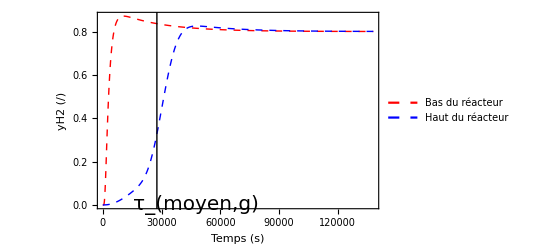

```mathematica
Plot[{yh2[10][t]/. sol,yh2[n-10/2][t]/. sol},{t,0,ψ τcg[Qg1,ϵs]},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"Temps (s)","yH2 (/)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotStyle->{Directive[Red,Dashed,Thick],Directive[Blue,Dashed,Thick]},
Epilog->{Directive[Black],Line[{{τcg[Qg1,ϵs],-0.1},{τcg[Qg1,ϵs],1.5}}],Text[Style["\!\(\*SubscriptBox[\(τ\), \(moyen,g\)]\)",20,Black],{τcg[Qg1,ϵs]+20000,0},{0,-1.5}]}]
```

## Profil C tot et y tot

50x3.5 Hill

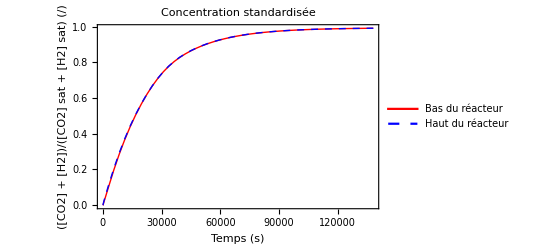

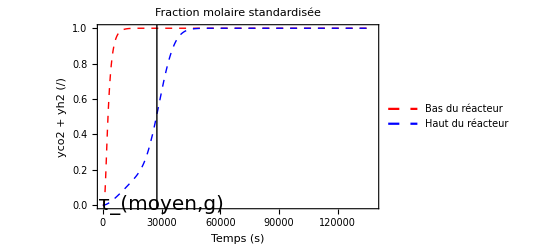

```mathematica
(*Absol[Ql1,Qg1,0.039,0.89,0.086,0.0265/60,0.0710/60]*)
ii[t_]=((Cco2[10][t])/(Hco2 Patm 0.2+Hh2 Patm 0.8)+(Ch2[10][t])/(Hco2 Patm 0.2+Hh2 Patm 0.8))/.sol;
jj[t_]=((Cco2[n-10][t])/(Hco2 Patm 0.2+Hh2 Patm 0.8)+(Ch2[n-10][t])/(Hco2 Patm 0.2+Hh2 Patm 0.8))/.sol;
kk[t_]=(yco2[10][t]+yh2[10][t])/.sol;
ll[t_]=(yco2[n-10][t]+yh2[n-10][t])/.sol;
Plot[{ii[t],jj[t]},{t,0,ψ τcg[Qg1,ϵs]},PlotRange->All, Frame->True,Axes->False,FrameLabel->{"Temps (s)","([CO2] + [H2])/([CO2] sat + [H2] sat) (/)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotLabel->"Concentration standardisée",
PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick]}]


Plot[{kk[t],ll[t]},{t,0,ψ τcg[Qg1,ϵs]},PlotRange->All, Frame->True,Axes->False,FrameLabel->{"Temps (s)","yco2 + yh2 (/)"},PlotLegends->Placed[{"Bas du réacteur","Haut du réacteur"},{Scaled[{0.95,0.02}],{Right,Bottom}}],PlotLabel->"Fraction molaire standardisée",
PlotStyle->{Directive[Red,Dashed,Thick],Directive[Blue,Dashed,Thick]},
Epilog->{Directive[Black],Line[{{τcg[Qg1,ϵs],-0.1},{τcg[Qg1,ϵs],1.5}}],Text[Style["\!\(\*SubscriptBox[\(τ\), \(moyen,g\)]\)",20,Black],{τcg[Qg1,ϵs]+2000,0},{0,-1.5}]}
]
```